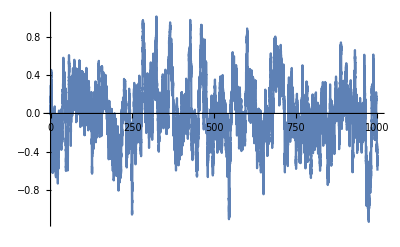

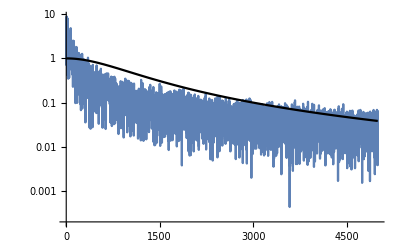

```mathematica
σ=0.2;
θ=0.2;
data=RandomFunction[OrnsteinUhlenbeckProcess[0,σ,θ],{0,1000,.05},1];
ListLinePlot[data,PlotRange->All,PlotStyle->Opacity[1]]
fdata=Fourier[data["Paths"][[1,;;,2]]];
Show[ListLogPlot[Abs[fdata[[;;5000]]],PlotRange->All,Joined->True],
LogPlot[σ^2/(θ^2+(ω/5000)^2),{ω,0,5000},PlotRange->All,PlotStyle->Black]]
```

```mathematica
fdata
```

{{3163.59+0. ⅈ,3162.54+0. ⅈ},{-4.31895-1005.21 ⅈ,1.15589-1009.47 ⅈ},1998,{-4.31895+1005.21 ⅈ,1.15589+1009.47 ⅈ}}
 |  |  |  |

```mathematica
data
```

TemporalData[…]

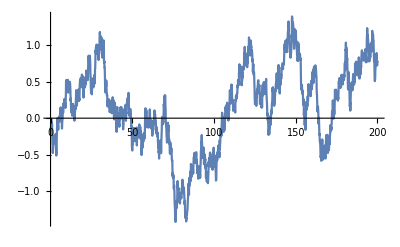

```mathematica
ListLinePlot[%74["Paths"][[1]]]
```